# TODA TBA

A short reference to the algorithm can be found in Section 3.1 of the appendix of https://arxiv.org/abs/2504.02044. For further questions, please contact me.

Toda’s thermodynamics has two “branches”, depending on the sign of the average stretch <r>_(P,V) . This code works only for the positive branch. It can be extended, but still to be done. Reference in 10.1088/1751-8121/ab2cf0

```mathematica
Clear["Global`*"]
```

### Parameters of the model (just run)

```mathematica
(* energy, derivative of the energy, momentum, derivative of the momentum*)
fϵ[λ_]:=0.5 λ^2;
fdϵ[λ_]:=λ;
fp[λ_]:=λ;
fdp[λ_]:=1;

(* primitive of the scattering kernel *)
fIϕ[λ_]:=2(λ*Log[Abs[λ]]-λ);

(* in Toda, the pressure is absorbed in the definition of the filling function, and it does not appear explicitly in the TBA equation. The normalization of the filling function is controlled by a chemical potential μ. As a matter of fact, the free energy turns out to be equal to this chemical potential F(P,V)= μ. Here we define the function for F(P,V) in thermal states (known from transferm matrix methods), and we will use it to control the pressure in the TBA *)
TodaF[β_,P_]:=Log[√(β/(2π))]+P Log[β]-Log[Gamma[P]];
```

### Functions for the code (just run)

```mathematica
(* this function computes all the bare quantities one needs*)
FBare[]:=(
p=Table[fp[1/2(λv[[i+1]]+λv[[i]])],{i,1,Length[λv]-1}];
dp=Table[fdp[1/2(λv[[i+1]]+λv[[i]])],{i,1,Length[λv]-1}];
ϵ=Table[fϵ[1/2(λv[[i+1]]+λv[[i]])],{i,1,Length[λv]-1}];
dϵ=Table[fdϵ[1/2(λv[[i+1]]+λv[[i]])],{i,1,Length[λv]-1}];
n=Table[1,{i,1,Length[λv]-1}];
Intv=Table[(λv[[i+1]]-λv[[i]]),{i,1,Length[λv]-1}];
charges=Table[Table[fcharges[1/2(λv[[i+1]]+λv[[i]])][[j]],{i,1,Length[λv]-1}],{j,1,nch}];
);

(* this function below computes th discretized integration kernel Φ *)
FΦ[]:=(
Iϕ[λ_]:=fIϕ[λ];
Φ=Table[Table[Iϕ[(λv[[j]]+λv[[j+1]])/2-λv[[i]]]-Iϕ[(λv[[j]]+λv[[j+1]])/2-λv[[i+1]]],{i,1,Length[λv]-1}],{j,1,Length[λv]-1}];);

(* this function takes a vector as an input, and it spits out the dressed vector. Needs to know the scattering kernel and filling function before*)
Dr[bare_]:=(
Return[LinearSolve[IdentityMatrix[Length[ϑ]]-Φ.DiagonalMatrix[ϑ],bare]];);

(*effective energy function that enters in the integral for the TBA*)
inputTBA[ε_]:=Exp[-ε];

(* solution of the tba at fixed lagrange multipliers. "betas" is a vector of size equal to the number of charges in the GGE *)
TBAch[betas_]:=(
Block[{x,Sol,source},

source=Sum[betas[[i]]*charges[[i]],{i,1,nch}];
Sol[x_]:=x-source+Φ.inputTBA[Table[x[[j]],{j,1,Length[Φ]}]];
ε=Re[Table[x[j],{j,1,Length[Φ]}]/.FindRoot[Sol[Table[x[j],{j,1,Length[Φ]}]],Table[{x[j],source[[j]]},{j,1,Length[Φ]}]]];

ϑ=Exp[-ε];];);


(* this is a plotting function. given an array of the vectors describing the tba functions (i.e. filling, roots or whatever) assigned to "in", it gives its plot as a function of the rapidity. For example in={p,ϵ} plots the momentum and energy in the same plot. If you want only a function, eg the energy, write in={ϵ},  Use "plrange" to change the plot range, and "name" for setting the label of the vertical axis*)
plot[in_,plrange_,name_]:=(
Return[ListPlot[Table[Table[{(λv[[i]]+λv[[i+1]])/2,in[[j]][[i]]},{i,1,Length[λv]-1}],{j,1,Length[in]}],PlotRange->plrange,Axes->False,Joined->True,Frame->True,FrameLabel->{"λ",name},InterpolationOrder->1]];

);
```

### Discretization of the rapidity space (need action)

To be sure that Λ is sufficiently large and npt enough for a good discretization. Λ=6 and npt=200 are good for a thermal state with β=1 and P=1.

```mathematica
Λ=6; (* rapidity cutoff*)
npt=400; (* number of points in the rapidity discretization*)

λv=N[Table[λ,{λ,-Λ,Λ,2Λ/(npt)}]];
dλ=λv[[2]]-λv[[1]];
```

## Running the TBA

### Choosing the GGE (need action)

Here I set the code for a thermal state. Can be generalized to GGEs.

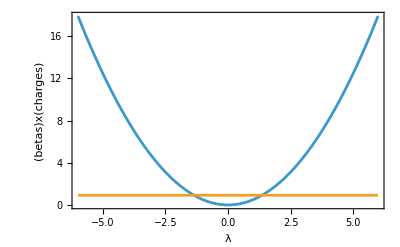

```mathematica
(* In this vector, put the charges you want in the GGE. In the current setup it is thermal*)
fcharges[λ_]:={fϵ[λ],-1};
nch=Length[fcharges[0]]; (* this just compute the number of conserved charges, it is an input needed for the code*)

T=1;
P=1;
betas={1/T,TodaF[1/T,P]}; 

FBare[];
in=Table[betas[[i]]*charges[[i]],{i,1,nch}];
Print[plot[in,All,"(betas)x(charges)"]];
```

## Run the TBA (just run)

```mathematica
FΦ[];
Print["Solving the TBA... "];
TBAch[betas];
Print["-- DONE --"];

dpdr=Dr[dp];
dϵdr=Dr[dϵ];
veff= dϵdr/dpdr;
ρt=dpdr;
 (* the first is the density of states over the volume, normalized to 1/<r> *) 
 (* the second is the density of states over the number of particles, normalized to 1 *) 
ρq=ϑ*dpdr;
Print["Average stretch: ",ν=1/Intv.ρq];
ρqN=ν*ϑ*dpdr;
Print["Density of energy over N = ", Intv.DiagonalMatrix[charges[[1]]].ρqN]
Print[P*ν/T];
(* Diffusion coefficient *)
Φdr = Table[Dr[Φ[[All,i]]],{i,1,Length[Φ]}];
veffKer=Table[Abs[veff[[i]]-veff[[j]]],{i,1,Length[veff]},{j,1,Length[veff]}];

(* dividing for the volume element since it is already inside the scattering kernel *)
Dv=Table[0.5/ρt[[i]]^2 Sum[  (veffKer[[i,j]] Φdr[[i,j]]^2 ρq[[j]])/Intv[[j]],{j,1,Length[Intv]}],{i,1,Length[Intv]}];
```

Solving the TBA...

-- DONE --

Average stretch: 0.577178

Density of energy over N = 1.5

0.577178

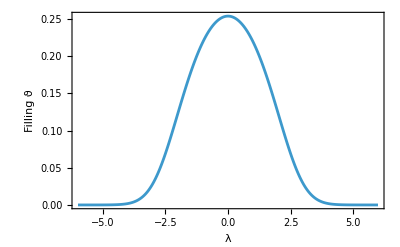

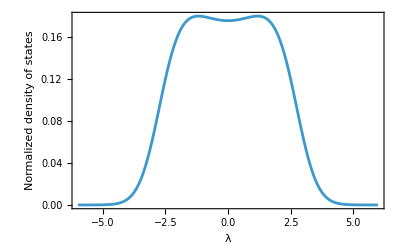

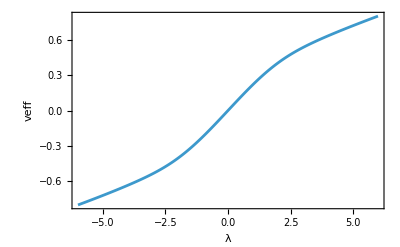

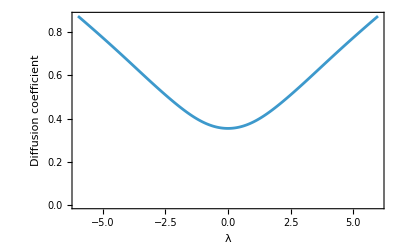

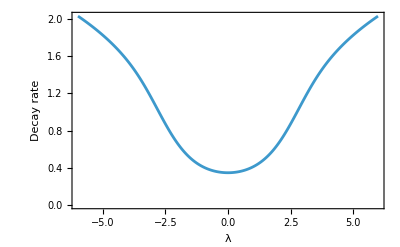

```mathematica
Print[plot[{ϑ},All,"Filling ϑ"]];
Print[plot[{ρqN},All,"Normalized density of states"]];
Print[plot[{veff},All,"veff"]];
Print[plot[{Dv},All,"Diffusion coefficient"]];
Print[plot[{(ν*ρt)/2},All,"Decay rate"]];
```

```mathematica
D0=0.5 ν Sum[Intv[[j]] ρt[[j]]^2 Abs[veff[[j]]] ρqN[[j]],{j,1,Length[Intv]}] (*Diffusion coefficient for Toda particle*)
```

0.605904

## Correlators

### Charge - Charge correlators (just run)

```mathematica
meas=ρqN; (* mesure appearing in the charge-charge correlators, depends on the statistics *)
corr[Q1_,Q2_]:=Return[Intv.DiagonalMatrix[Q1*Q2].meas]

chargesdr=Table[Dr[charges[[i]]],{i,1,nch}]; (* dressing the bare charges *)
Cm=Table[corr[chargesdr[[i]],chargesdr[[j]]],{i,1,nch},{j,1,nch}]; (* static covariance matrix *)

Print["Static covariance matrix C: ",Cm//Chop//MatrixForm];
```

Static covariance matrix C: (4.27125 | -1.47467
-1.47467 | 1.07024)